### Discontinuous Galerkin Method for Rank k

```mathematica
$Path=Join[$Path,{"~/Documents/Sparse\ Grids/Hierarchical\ Galerkin\ Method/"}];
```

```mathematica
<<Methods.m
```

### Discontinuous Galerkin Calculations

```mathematica
coeffsk=fullCoefficientsk[4,Sin[Pi #]&,4]//Quiet
```

SparseArray[<64>, {4, 5, 8}]

### Comparision of All Errors

```mathematica
dg1Error=Table[Sqrt[.0062 Sum[(reconstructk[1,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[1,Sin[Pi #]&,n]],{n,1,8}]//Quiet
dg2Error=Table[Sqrt[.0062 Sum[(reconstructk[2,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[2,Sin[Pi #]&,n]],{n,1,7}]//Quiet
dg3Error=Table[Sqrt[.0062 Sum[(reconstructk[3,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[3,Sin[Pi #]&,n]],{n,1,6}]//Quiet
dg4Error=Table[Sqrt[.0062 Sum[(reconstructk[4,#,x,n]-Sin[Pi x])^2,{x,0,1,.0062}]&@fullCoefficientsk[4,Sin[Pi #]&,n]],{n,1,5}]//Quiet
```

{0.310658,0.161549,0.0813504,0.0407878,0.0205338}

{0.0632198,0.015956,0.00401919,0.00100416,0.000247567}

{0.00853766,0.00112029,0.00014118,0.0000179772,2.38176×10^-6}

{0.000846151,0.0000520552,3.26065×10^-6,2.00796×10^-7,1.21776×10^-8}

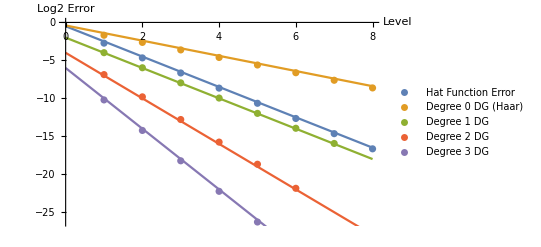

```mathematica
Show[ListPlot[{hatError,dg1Error,dg2Error,dg3Error,dg4Error}//Log2,PlotLegends->{"Hat Function Error", "Degree 0 DG (Haar)","Degree 1 DG","Degree 2 DG","Degree 3 DG"},AxesLabel->{"Level","Log2 Error"}],Plot[{-2x-.5,-x-.4,-2x-2,-3x-4,-4x-6},{x,0,8}]]
```